```mathematica
y[t_]:= 1. - Exp[-10.*((t) + ArcTan[t])]
```

```mathematica
filembe0 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mbe0.dat";
filembe1 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mbe1.dat";
filembe2 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mbe2.dat";
filempe0 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mpe0.dat";
filempe1 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mpe1.dat";
filempe2 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mpe2.dat";
filemt0 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mt0.dat";
filemt1 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mt1.dat";
filemt2 = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mt2.dat";
errmbe = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\errors_mbe.dat";
errmpe = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\errors_mpe.dat";
errmt = "G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\errors_mt.dat";
```

```mathematica
mbe0 = ReadList[filembe0, {Real, Real}];
mbe1 = ReadList[filembe1, {Real, Real}];
mbe2 = ReadList[filembe2, {Real, Real}];
mpe0 = ReadList[filempe0, {Real, Real}];
mpe1 = ReadList[filempe1, {Real, Real}];
mpe2 = ReadList[filempe2, {Real, Real}];
mt0 = ReadList[filemt0, {Real, Real}];
mt1 = ReadList[filemt1, {Real, Real}];
mt2 = ReadList[filemt2, {Real, Real}];
embe = ReadList[errmbe, {Real, Real}];
empe = ReadList[errmpe, {Real, Real}];
emt = ReadList[errmt, {Real, Real}];
```

ReadList::nffil: File not found during ReadList["G:\\Studia\\IV\\MO\\Laboratoria\\10\\Program10\\Program10\\results_mt2.dat", {Real, Real}].

```mathematica
"Metoda bezposrednia Euler'a:"
dp1 = (Abs[Part[Part[embe,12], 2]-Part[Part[embe,25], 2]]) / (Abs[Part[Part[embe, 12], 1] - Part[Part[embe,25], 1]])
```

Metoda bezposrednia Euler'a:

1.00088

```mathematica
"Metoda posrednia Euler'a:"
dp2 = (Abs[Part[Part[empe,12], 2]-Part[Part[empe,25], 2]]) / (Abs[Part[Part[empe, 12], 1] - Part[Part[empe,25], 1]])
```

Metoda posrednia Euler'a:

0.999127

```mathematica
"Metoda posrednia trapezow:"
dp3 = (Abs[Part[Part[emt,12], 2]-Part[Part[emt,25], 2]]) / (Abs[Part[Part[emt, 12], 1] - Part[Part[emt,25], 1]])
```

Metoda posrednia trapezow:

2.00057

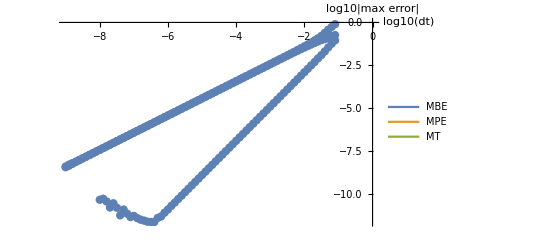

```mathematica
ListLinePlot[{embe, empe, emt},AxesLabel->{"log10(dt)", "log10|max error|"}, PlotLegends->{"MBE", "MPE", "MT"}, Mesh->All]
```

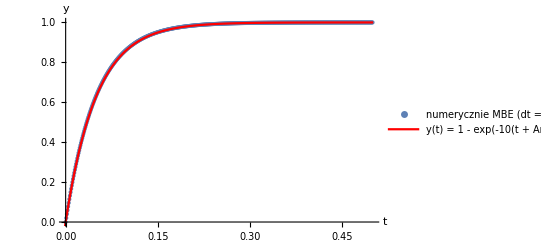

```mathematica
Show[ListPlot[mbe0,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MBE (dt = 10e-3)"}], Plot[y[t], {t, -0.5, 0.5}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

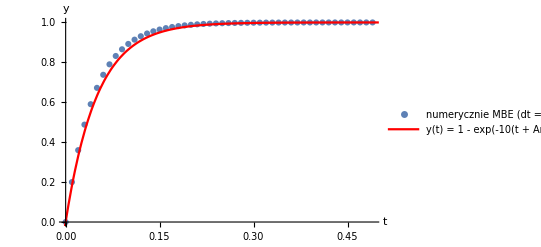

```mathematica
Show[ListPlot[mbe1,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MBE (dt = 10e-2)"}], Plot[y[t], {t, -0.5, 0.5}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

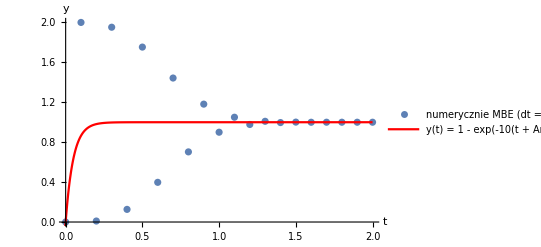

```mathematica
Show[ListPlot[mbe2,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MBE (dt = 10e-1)"}], Plot[y[t], {t, -0.5, 2}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

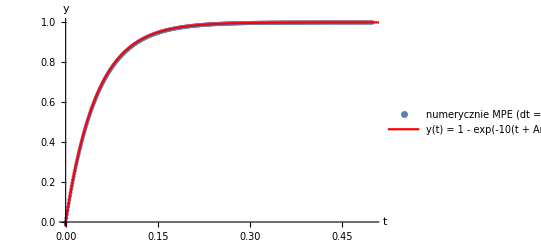

```mathematica
Show[ListPlot[mpe0,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MPE (dt = 10e-3)"}], Plot[y[t], {t, -0.5, 2}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

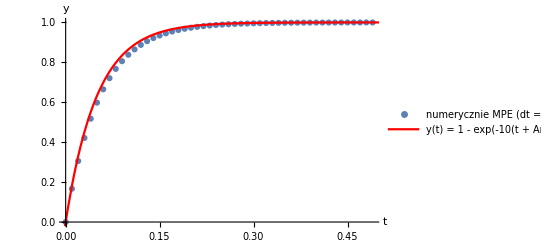

```mathematica
Show[ListPlot[mpe1,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MPE (dt = 10e-2)"}], Plot[y[t], {t, -0.5, 2}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

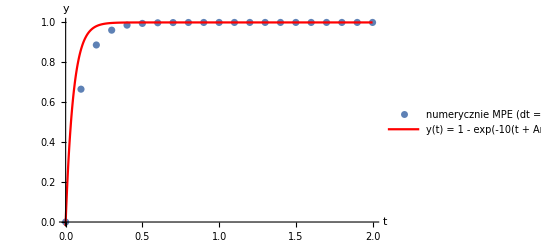

```mathematica
Show[ListPlot[mpe2,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MPE (dt = 10e-1)"}], Plot[y[t], {t, -0.5, 2}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

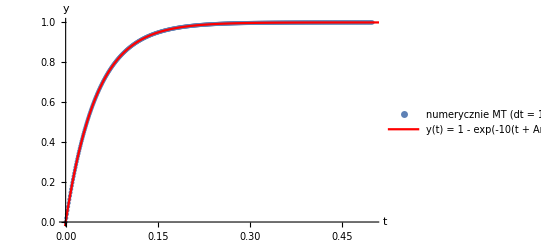

```mathematica
Show[ListPlot[mt0,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MT (dt = 10e-3)"}], Plot[y[t], {t, -0.5, 2}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

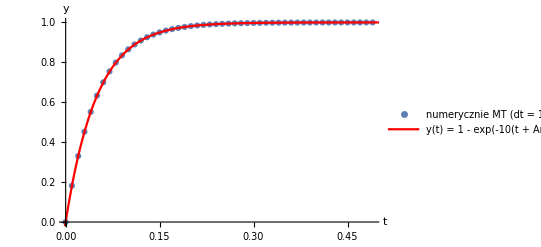

```mathematica
Show[ListPlot[mt1,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MT (dt = 10e-2)"}], Plot[y[t], {t, -0.5, 2}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ListPlot[$Failed, AxesLabel → {.

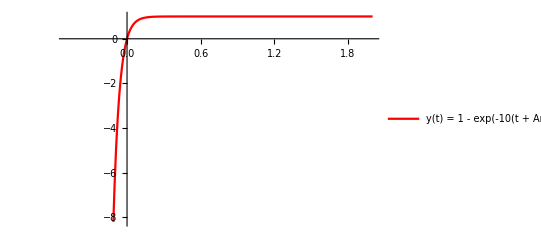
Show[ListPlot[$Failed,AxesLabel→{t,y},PlotLegends→{numerycznie MT (dt = 10e-1)}],-Graphics-]

```mathematica
Show[ListPlot[mt2,AxesLabel->{"t", "y"}, PlotLegends->{"numerycznie MT (dt = 10e-1)"}], Plot[y[t], {t, -0.5, 2}, PlotLegends->{"y(t) = 1 - exp(-10(t + ArcTan(t)))"}, PlotStyle->{Red}]]
```